```mathematica
L=313.328*10^-6 ;  (*电感*)
c=1600*10^-6;(*电容*)
R=0.4;(*电阻*)
r=0.01;(*线圈内径*)
d0=0.001;(*铜丝直径*)
d=0.006;(*亚克力内直径*)(*电流用J表示*)
l=0.035;(*弹丸长度*)
m=0.007;(*子弹质量*)
Rd=0.4;(*二极管近似电阻*)
Vi=0;(*初速度*)
Xi=-0.03;(*初始位置*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

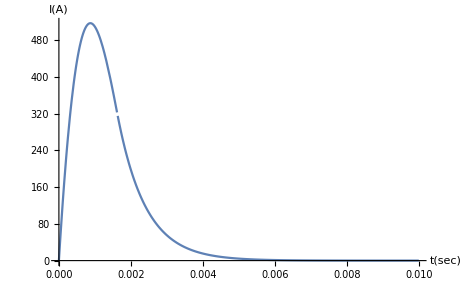

-Graphics3D-

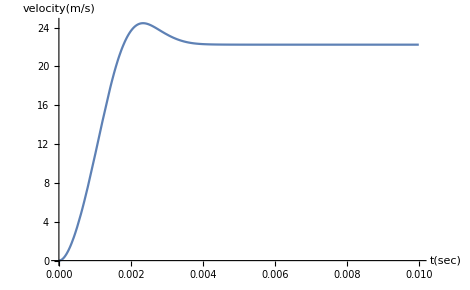

```mathematica
(*计算电流*)
{Itt}=Simplify[-c*U'[t1]/.DSolve[{L*c*U''[t1]+R*c*U'[t1]+U[t1]==0,U[0]==400,U'[0]==0},U,t1]];
{Utt}=Simplify[U[t1]/.DSolve[{L*c*U''[t1]+R*c*U'[t1]+U[t1]==0,U[0]==400,U'[0]==0},U,t1]];
It1[t_]:=Itt/.t1->t;(*LRC振荡*)
Ut1[t_]:=Utt/.t1->t;
{t3,t2}=x/.Solve[Ut1[x]==0];(*解出电压为0时的t*)
It2[t_]:=It1[t2]*Exp[-Rd/L*(t-t2)];(*LR放电*)
It[t_]:=Piecewise[{{It1[t],t≤t2},{It2[t],t≥t2}}];(*分段合成后的电流*)
Plot[It[t],{t,0,0.01},AxesLabel->{"t(sec)","I(A)"}]
H[x_,t_]:=∑_(i=1)^8 ∑_(k=-13)^14 1/(2*((r+(i-1/2)*d0)^2+(x-k*d0)^2)^(3/2))*It[t]*(r+(i-1/2)*d0)^2
Plot3D[H[x,t],{x,-0.07,0.07},{t,0,0.01},PlotRange->All]
F=NDSolve[{(π*d^2*1.8)/4*(H[xc[t]+l/2,t]-H[xc[t]-l/2,t])==m*xc''[t],xc[0]==Xi,xc'[0]==Vi},xc,{t,0,0.01}];
Plot[Evaluate[D[xc[t],t]/.F],{t,0,0.01},PlotRange->All,AxesLabel->{"t(sec)","velocity(m/s)"}]
```

```mathematica
(*末速与初始位置分析*)
```

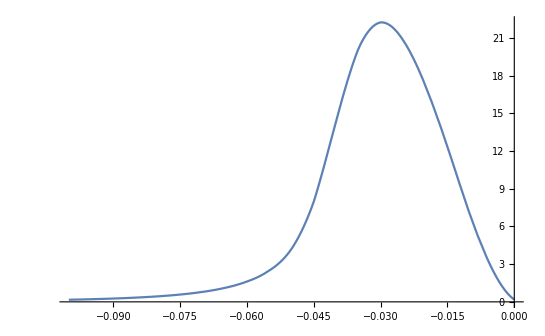

```mathematica
data1=Flatten[Table[xc'[0.01]/.NDSolve[{(π*d^2*1.8)/4*(H[xc[t]+l/2,t]-H[xc[t]-l/2,t])==m*xc''[t],xc[0]==a,xc'[0]==Vi},xc,{t,0,0.01}],{a,-0.12,0,0.005}]];
data2=Table[a,{a,-0.12,0,0.005}];
data={data2,data1}//Transpose;
Va=Interpolation[data];
Plot[Va[a],{a,-0.1,0}]
```

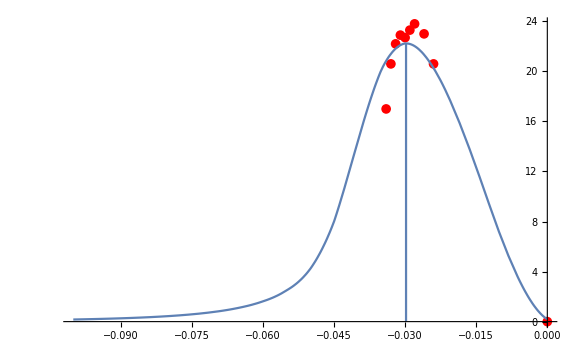

```mathematica
data5={{-0.034,17.},{-0.033,20.6},{-0.032,22.2},{-0.031,22.9},{-0.03,22.7},{-0.029,23.3},{-0.028,23.8},{-0.026,23.},{-0.024,20.6},{0,0}};
Maxf={x/.FindMaximum[Va[x],{x,-0.1,-0.001}][[2]],FindMaximum[Va[x],{x,-0.1,-0.001}][[1]]};
Show[
ListPlot[data5,PlotStyle->{Red,PointSize[0.012]}],
Plot[Va[a],{a,-0.1,0}],
ParametricPlot[{Maxf[[1]],y},{y,0,Maxf[[2]]}],
PlotRange->All
]
```

```mathematica
(*red points are actual ejecting speed measured by photogate
while the blue curve is the predicting line*)
```